# Basis functions for C3

Bravais lattice:

```mathematica
a1={Cos[π/6],Sin[π/6]};
a2={Cos[π/6],-Sin[π/6]};
```

```mathematica
a1
```

{(√3)/2,1/2}

Reciprocal lattice vectors:

```mathematica
b1=2π *(RotationMatrix[π/2].a2)/(a1.RotationMatrix[π/2].a2)
b2=2π *(RotationMatrix[π/2].a1)/(a2.RotationMatrix[π/2].a1)
{a1.b1,a2.b2,a1.b2,a2.b1}
```

{(2 π)/(√3),2 π}

{(2 π)/(√3),-2 π}

{2 π,2 π,0,0}

```mathematica
Dir=b1+(b1+b2);
C1=Norm[b1]/(2Cos[π/6])*Dir/Norm[Dir];
Γp={0,0};
Mp={C1[[1]],0};
Kp=C1;
```

We need to start with a reasonable “seed function”:

```mathematica
X[kx_,ky_]=-4/3(Cos[a1.{kx,ky}]+Cos[a2.{kx,ky}]-2 Cos[(a1-a2).{kx,ky}])//FullSimplify
(*X[kx_,ky_]=4/9(-2 Cos[(a1+a2).{kx,ky}]+(Cos[(2a1-a2).{kx,ky}]+Cos[(2a2-a1).{kx,ky}]))//FullSimplify;*)
Xv[k_]:=X[k[[1]],k[[2]]]
Xv[{0,0}]
Y[kx_,ky_]=-2/(√3)(Xv[{kx,ky}]/2+Xv[RotationMatrix[-2π/3].{kx,ky}])//FullSimplify
```

8/3 (-Cos[(√3 kx)/2] Cos[ky/2]+Cos[ky])

0

(8 Sin[(√3 kx)/2] Sin[ky/2])/(√3)

Note that, in terms of hopping parameters, this corresponds to

```mathematica
4/3*√3(Cos[a2.{kx,ky}]-Cos[a1.{kx,ky}])//FullSimplify
```

(8 Sin[(√3 kx)/2] Sin[ky/2])/(√3)

Let’s check whether we have indeed found the right behavior:

```mathematica
Yv[k_]:=Y[k[[1]],k[[2]]]
RotationMatrix[2π/3].{Xv[{kx,ky}],Yv[{kx,ky}]}-{Xv[RotationMatrix[-2π/3].{kx,ky}],Yv[RotationMatrix[-2π/3].{kx,ky}]}//FullSimplify
{Xv[{kx,ky}],Yv[{kx,ky}]}-{Xv[{kx,-ky}],-Yv[{kx,-ky}]}//FullSimplify
```

{0,0}

{0,0}

So these particular basis functions are also partner functions of E of D3.

Let’s plot them as they are:

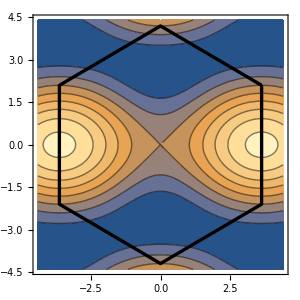
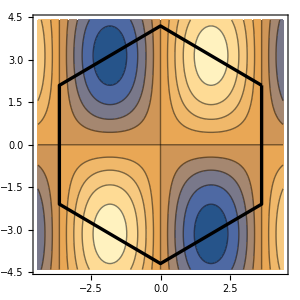

```mathematica
Scl=1.4;
{Show[ContourPlot[Xv[{kx,ky}],{kx,-π  Scl,π Scl},{ky,-π Scl,π Scl},ImageSize->300],Graphics[{Thickness[0.008],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]]}]],Show[ContourPlot[Yv[{kx,ky}],{kx,-π  Scl,π Scl},{ky,-π Scl,π Scl},ImageSize->300],Graphics[{Thickness[0.008],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]]}]]}
```

And let’s expand them:

a) Around the Γ point:

```mathematica
Series[Xv[{α kx,α ky}],{α,0,2}]//FullSimplify
Series[Yv[{α kx,α ky}],{α,0,2}]//FullSimplify
```

(kx^2-ky^2) α^2+O[α]^3

2 kx ky α^2+O[α]^3

b) Around the K point:

```mathematica
Series[Xv[{α kx,α ky}+Kp],{α,0,1}]//FullSimplify
Series[Yv[{α kx,α ky}+Kp],{α,0,1}]//FullSimplify
```

2 √3 ky α+O[α]^2

-2 (√3 kx) α+O[α]^2

c) Around the K’ point:

```mathematica
Series[Xv[{α kx,α ky}+{Kp[[1]],-Kp[[2]]}],{α,0,1}]//FullSimplify
Series[Yv[{α kx,α ky}+{Kp[[1]],-Kp[[2]]}],{α,0,1}]//FullSimplify
```

-2 (√3 ky) α+O[α]^2

2 √3 kx α+O[α]^2

Export for the notes:

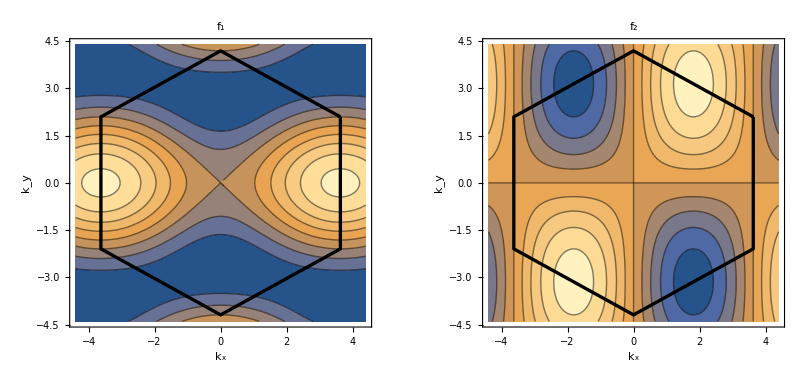

```mathematica
GraphicsGrid[{{Show[ContourPlot[Xv[{kx,ky}],{kx,-π  Scl,π Scl},{ky,-π Scl,π Scl},ImageSize->300,FrameLabel->{"k_x","k_y"},PlotLabel->"f_1"],Graphics[{Thickness[0.008],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]]}]],Show[ContourPlot[Yv[{kx,ky}],{kx,-π  Scl,π Scl},{ky,-π Scl,π Scl},ImageSize->300,FrameLabel->{"k_x","k_y"},PlotLabel->"f_2"],Graphics[{Thickness[0.008],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]]}]]}}]
```